```mathematica
x1[R_, r_, θ_, φ_] := (R + r Cos[θ]) Cos[φ];
x2[R_, r_, θ_, φ_] := (R + r Cos[θ]) Sin[φ];
x3[R_, r_, θ_, φ_] := r Sin[θ];
x[R_, r_, θ_, φ_] := { x1[R,r,θ, φ], x2[R,r,θ, φ], x3[R,r,θ, φ]}
```

```mathematica
d1[R_, r_, θ_, φ_] = D[x[R,r,θ, φ], θ];
d2[R_, r_, θ_, φ_] = D[x[R,r,θ, φ], φ];
J[R_, r_, θ_, φ_] =  Norm[Cross[d1[R,r,θ, φ], d2[R,r,θ, φ]]] //FullSimplify
```

Abs[r] Abs[R+r Cos[θ]] √(Abs[Sin[θ]]^2+Abs[Cos[θ]]^2 (Abs[Cos[φ]]^2+Abs[Sin[φ]]^2))

```mathematica
dist[θ1_, φ1_, θ2_, φ2_, R_, r_]:= Norm[x[R,r, θ1, φ1] - x[R,r, θ2, φ2]];
ker[θ1_, φ1_,  θ2_,φ2_, R_, r_] := dist[θ1, φ1, θ2,φ2, R, r]^-2;
ker[0,0,0,Pi/2, R,r]
```

1/((Abs[-r-R]^2+Abs[r+R]^2)^2)

```mathematica
Integrate[ker[ x,y,  θ1, φ1,  1, 0.2] *Cos[θ1]*Cos[φ1] ,{θ1, 0,2 π},{φ1, 0, 2 π}]
```

∫_0^(2 π) ∫_0^(2 π) (Cos[θ1] Cos[φ1])/((Abs[(1+0.2 Cos[x]) Cos[y]+(-1-0.2 Cos[θ1]) Cos[φ1]]^2+Abs[0.2 Sin[x]-0.2 Sin[θ1]]^2+Abs[(1+0.2 Cos[x]) Sin[y]+(-1-0.2 Cos[θ1]) Sin[φ1]]^2)^2)ⅆφ1ⅆθ1

```mathematica
Manipulate[Plot3D[(2/3) π^2 r(8 π^2 +48 r + (3+12 π^2)r^2+24 r^3+(8 π^2 r+24 r^2) Cos[x]+(-24-12 r^2) Cos[y] + (-12 r^3 -24r) Cos[x]Cos[y]),{x,-7.40,7.40},{y,-10.86,10.86}], {r,-2,2}]
```

```mathematica
Evaluate[ker[ 0.0,0.0,  θ1, φ1,  1, 0.2]*0.2 (1+0.2 Cos[θ1]) * Cos[φ1] ]
```

0.2 (Abs[1.2-(1+0.2 Cos[θ1]) Cos[φ1]]^2+Abs[0.-0.2 Sin[θ1]]^2+Abs[0.-(1+0.2 Cos[θ1]) Sin[φ1]]^2) (1+0.2 Cos[θ1]) Cos[φ1]

```mathematica
ker[ 0.0, 0.0,2* 2π/10, 3* 2π/10, 1, 0.2]
```

3.39108

```mathematica
Norm[x[1, 0.2, 0,0] - x[1,0.2, 2* 2π/10, 3* 2π/10]]^2
```

3.39108

```mathematica
dist[θ1, θ2, φ1, , 1, 0.2]
```

```mathematica
Plot3D[(x-π)^2+(y-π)^2,{x,0,2π},{y,0,2 π}]
```

-Graphics3D-

```mathematica
f[x_,y_]:=(x^3-x)(y^3-y); K[x1_,y1_,x2_,y2_]:= (Sin[x1-x2]^2-Sin[y1-y2]^2);
```

```mathematica
Integrate[K[x,y,x2,y2] f[x2,y2], {x2,0,1},{y2,0,1}]
```

```mathematica
f[x_,y_]:= Min[
Integrate[Exp[-(x-2)^2] Exp[x^2](x-x^3), {x,0,1}]
```

1/128 (7+5/ⅇ^4)

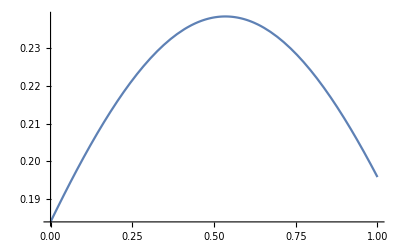

```mathematica
Plot[1/4 ⅇ^(-1-u^2) (-2 ⅇ u^2+2 ⅇ^(2 u) (1+u+u^2)+ⅇ^(1+u^2) √π (u+2 u^3) (-2+Erfc[1-u]+Erfc[u])),{u,0,1}]
```

```mathematica
Plot3D[(x-x^3)(y-y^3), {x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Evaluate[Exp[x^2+ y^2](x-x^3)(y-y^3), x=0.2,y=0.7]
```

```mathematica
Clear[x]
```

```mathematica
Integrate[Exp[-(1-u+y)]Exp[y](y-y^3), {y,0, u-1/2}]
```

-1/64 ⅇ^(-1+u) (1-2 u)^2 (-7-4 u+4 u^2)

```mathematica
Integrate[Exp[-(u-y)]Exp[y](y-y^3), {y, u-1/2,u }]
```

1/8 ⅇ^(-1+u) (-4+ⅇ-2 ⅇ (-1+u) u (-1+2 u)+u (11+4 (-3+u) u))

```mathematica
Integrate[Exp[-(y-u)]Exp[y](y-y^3), {y, u,1}]
```

```mathematica
ⅇ^u/4-(ⅇ^u u^2)/2+(ⅇ^u u^4)/4 + 1/8 ⅇ^(-1+u) (-4+ⅇ-2 ⅇ (-1+u) u (-1+2 u)+u (11+4 (-3+u) u)) + -1/64 ⅇ^(-1+u) (1-2 u)^2 (-7-4 u+4 u^2)
```

ⅇ^u/4-(ⅇ^u u^2)/2+(ⅇ^u u^4)/4-1/64 ⅇ^(-1+u) (1-2 u)^2 (-7-4 u+4 u^2)+1/8 ⅇ^(-1+u) (-4+ⅇ-2 ⅇ (-1+u) u (-1+2 u)+u (11+4 (-3+u) u))

```mathematica
FullSimplify[ⅇ^u/4-(ⅇ^u u^2)/2+(ⅇ^u u^4)/4-1/64 ⅇ^(-1+u) (1-2 u)^2 (-7-4 u+4 u^2)+1/8 ⅇ^(-1+u) (-4+ⅇ-2 ⅇ (-1+u) u (-1+2 u)+u (11+4 (-3+u) u))]
```

1/64 ⅇ^(-1+u) (-25+8 u (8+u (-11-2 (-4+u) u))+8 ⅇ (3+2 u (-1+(-1+u)^2 u)))

```mathematica
FullSimplify[(7 ⅇ^u)/32+(3 ⅇ^u u)/4-(3 ⅇ^u u^2)/4-ⅇ^u u^3+1/8 ⅇ^-u (ⅇ+ⅇ^(2 u) (-1-u+4 u^3))]
```

1/32 ⅇ^-u (4 ⅇ+ⅇ^(2 u) (3-4 u (-5+6 u+4 u^2)))

```mathematica
FullSimplify[9 ⅇ^(-1+x)+x-x (5+(-3+x) x)-x (6+x (3+x))+(25+2 x (11+6 x+4 x^2))/(8 √ⅇ)+(-67+2 x (35+2 x (-9+2 x)))/(8 √ⅇ)]
```

```mathematica
Evaluate[9 ⅇ^(-1+x)+((-1+2 x) (21+4 (-1+x) x))/(4 √ⅇ)-2 x (5+x^2) , x=0.70000000]
```

Sequence[0.20413,0.7]

```mathematica
FullSimplify[-5 ⅇ^(-1+x)+(25+22 x+12 x^2+8 x^3)/(8 √ⅇ)]
```

```mathematica
-3 ⅇ^-x-2 x (5+x^2)+((1+2 x) (21+4 x (1+x)))/(4 √ⅇ)
```

```mathematica
Evaluate[-3 ⅇ^-x-2 x (5+x^2)+((1+2 x) (21+4 x (1+x)))/(4 √ⅇ), x=0.200000]
```

Sequence[0.189602,0.2]

```mathematica
Integrate[Exp[-(1-y)], {y, 1/2, 1}]
```

```mathematica
(1-1/(√ⅇ))*2
```

2 (1-1/(√ⅇ))

```mathematica
N[2 (1-1/(√ⅇ))]
```

0.786939